# 2 - Graphics primitives

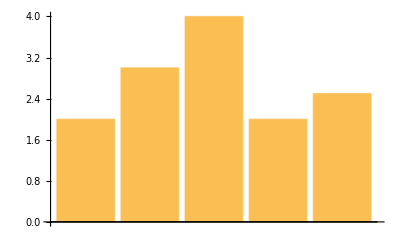

```mathematica
BarChart[{2,3,4,2,2.5}]
```

All graphics in Mathematica are built from a few simple geometric shapes, such as circles, rectangles and lines. These are called graphics primitives. Functions such as BarChart and ListPlot create plots by arranging those shapes to construct the corresponding charts. In many cases these built-in functions are all we need, but there are scenarios where we may want to construct some custom chart that cannot be obtained from Mathematica’s pre-defined functions. In those cases, we need to build a chart from scratch by using graphics primitives.

Another use for graphics primitives is to add annotations to charts. For example, we may want to draw an arrow to call attention to a particularly interesting data point in a line plot, or we may want to draw a transparent rectangle to highlight a region of a scatter plot. These chart annotations are especially important in explanatory data visualisation.

In the following, we will learn to use the graphics primitives to create new kinds of charts from scratch, and to annotate plots.

## A tour of graphics primitives

An example of a graphics primitive is a circle. Circle[{x,y}, r] represents a circle with radius r centred at point {x,y}. However, by itself Circle does nothing:

```mathematica
Circle[{0,0}, 1]
```

Circle[{0,0},1]

Graphics primitives are only displayed inside a Graphics command:



```mathematica
Graphics[Circle[{0,0}, 1]]
```

We can plot multiple shapes by passing a list to Graphics:

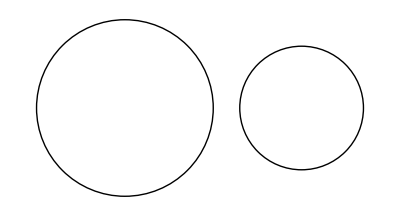

```mathematica
Graphics[{Circle[{0,0}, 1], Circle[{2,0}, 0.7]}]
```

Here are the most important graphics primitives:

Circle[{x,y}, r] | circle of radius r centred at {x,y}
Disk[{x,y}, r] | disk of radius r centred at {x,y}
Rectangle[{x_1,y_1},{x_2,y_2}] | rectangle with corners {x_1,y_1},{x_2,y_2}
Polygon[{{x_1,y_1}, ...}] | polygon with corners {x_1,y_1}, ...
Line[{{x_1,y_1}, ...}] | lines connecting points {x_1,y_1},... 
Arrow[{{x_1,y_1}, ...}] | like Line,but with an arrow at the end
Point[{x,y},...] | points at positions {x,y},...
Text[txt, {x,y}] | text txt at position {x,y}

Here is an example showing all these primitives being used:

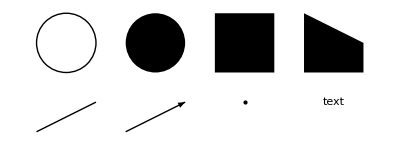

```mathematica
Graphics[{
	Circle[{0,3}, 1],
	Disk[{3,3}, 1],
	Rectangle[{5,2}, {7,4}],
	Polygon[{{8,2}, {8,4}, {10,3}, {10,2}}],
	Line[{{-1,0}, {1,1}}],
	Arrow[{{2,0}, {4,1}}],
	Point[{6,1}],
	Text["text", {9,1}]
}]
```

Of course, we are not limited to manually list the graphics primitives; we can use Mathematica’s list manipulation functions to generate them for us:

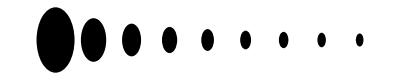

```mathematica
Graphics[Table[Disk[{n, 0}, 1/n], {n, 2, 10}]]
```

### Graphics directives

We can customise how the graphics primitives are drawn by using graphics directives. For example, we can set the colour:

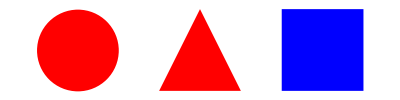

```mathematica
Graphics[{
	Red, 
	Disk[{0,0}, 1], 
	Polygon[{{2,-1},{4,-1},{3,1}}], 
	Blue, 
	Rectangle[{5,-1}, {7,1}]
}]
```

The first object in the list above (Red), does not draw anything; it just sets the colour that will be used in drawing from that point on. So the next two objects in the list are red. Then we have Blue, which resets the drawing colour to blue. The last element in the list, Rectangle, is therefore coloured blue.

We can bind graphics directives to a set of objects by grouping directives and objects in lists:

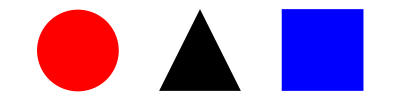

```mathematica
Graphics[{
	{Red, Disk[{0,0}, 1]}, 
	Polygon[{{2,-1},{4,-1},{3,1}}], 
	{Blue, Rectangle[{5,-1}, {7,1}]}
}]
```

Here is a table of the most important graphics directives:

Red, Green, Blue
RGBColor[r,g,b,a] | Set colour
PointSize[d] | Set point size
Thick, Thin
Thickness[d] | Set line thickness
Dashed, Dotted, DotDashed
Dashing[d] | Set dashing pattern of lines
GrayLevel[s] | Set gray level

Here is an example using many of these directives:

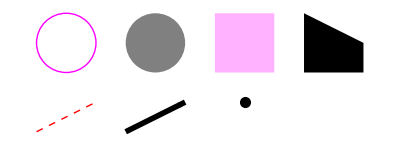

```mathematica
Graphics[{
	{RGBColor[1,0,1], Circle[{0,3}, 1]},
	{GrayLevel[0.5], Disk[{3,3}, 1]},
	{RGBColor[1,0,1,0.3], Rectangle[{5,2}, {7,4}]},
	Polygon[{{8,2}, {8,4}, {10,3}, {10,2}}],
	{Thick, Dashed, Red, Line[{{-1,0}, {1,1}}]},
	{Thickness[0.01], Arrow[{{2,0}, {4,1}}]},
	{PointSize[0.02], Point[{6,1}]}
}]
```

### Options of Graphics

The command Graphics accepts most of the options you are used to in Mathematica plotting functions:

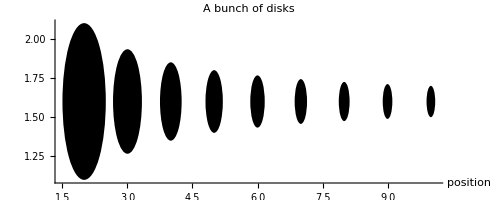

```mathematica
Graphics[Table[Disk[{n, 1.6}, 1/n], {n, 2, 10}],
	AxesLabel->{"position", None},
	PlotLabel->"A bunch of disks",
	Axes->{True,False}]
```

By default, Graphics does not plot axes, so you must enable them by setting the Axes option if you want them.

## Using graphics primitives to annotate plots

One of the uses of graphics primitives is to add extra information to plots. Let us use a line plot of the temperatures measured in London in January 2015 as an example:

```mathematica
Entity["City",{"London","GreaterLondon","UnitedKingdom"}]//InputForm
```

Entity["City", {"London", 
  "GreaterLondon", 
  "UnitedKingdom"}]

```mathematica
tempLondon = Table[{day, AirTemperatureData[Entity["City",{"London","GreaterLondon","UnitedKingdom"}], {2015,1,day, 13,0,0}, 
                                       UnitSystem->"Metric"]},
             {day, 1, 30}]
```

{{1,9. °C},{2,9. °C},{3,6. °C},{4,2. °C},{5,10. °C},{6,11. °C},{7,9. °C},{8,9. °C},{9,13. °C},{10,11. °C},{11,9. °C},{12,12. °C},{13,9. °C},{14,7. °C},{15,8. °C},{16,6. °C},{17,7. °C},{18,4. °C},{19,4. °C},{20,4. °C},{21,3. °C},{22,5. °C},{23,5. °C},{24,6. °C},{25,9. °C},{26,10. °C},{27,9. °C},{28,8. °C},{29,6. °C},{30,6. °C}}

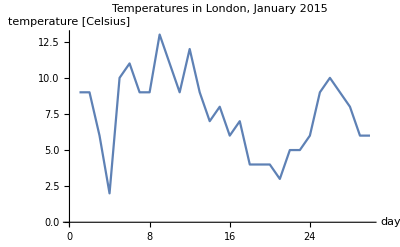

```mathematica
ListLinePlot[tempLondon, 
	PlotLabel->"Temperatures in London, January 2015",
	AxesLabel->{"day", "temperature [Celsius]"}
]
```

It is useful to show the average temperature during the period depicted in the plot. Let us draw a straight line indicating where the average is:

```mathematica
Mean[tempLondon]⟦2⟧//QuantityMagnitude
```

7.53333

```mathematica
Mean[tempLondon] ⟦2⟧ // QuantityMagnitude // N
```

7.53333

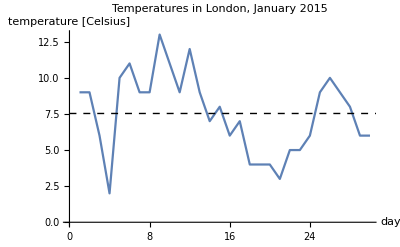

```mathematica
avgTemp = Mean[tempLondon]⟦2⟧ // QuantityMagnitude;
ListLinePlot[tempLondon, 
	PlotLabel->"Temperatures in London, January 2015",
	AxesLabel->{"day", "temperature [Celsius]"},
	Epilog->{
		Dashed, 
		Line[{{0,avgTemp}, {31,avgTemp}}]
	}
]
```

You can add graphics primitives to a plot by setting the plot’s Epilog option to the list of primitives and directives you want to superimpose on the plot. You can also use the Prolog option, which draws the primitives before the rest of the plot is drawn. In most cases, you should use the Epilog. 

This new version of the plot allows us to easily see which days had above or below average temperatures. But there is a problem: nowhere in the plot is it indicated that the dashed line means the average temperature. We can indicate this by adding a text graphics primitive:

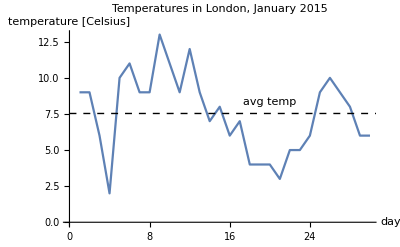

```mathematica
avgTemp = Mean[tempLondon]⟦2⟧ // QuantityMagnitude;
ListLinePlot[tempLondon, 
	PlotLabel->"Temperatures in London, January 2015",
	AxesLabel->{"day", "temperature [Celsius]"},
	Epilog->{
		Dashed, 
		Line[{{0,avgTemp}, {31,avgTemp}}],
	    Text["avg temp", {20, avgTemp+0.8}]
	}
]
```

It is often important to display the expected fluctuation around the average. This is most commonly measured by the standard deviation:

```mathematica
stdDevTemp = StandardDeviation[tempLondon]⟦2⟧ // N
```

2.7384 °C

We could represent the range of temperatures we would expect to see as a pair of lines surrounding the average value, placed above and below it, and shifted by one standard deviation:

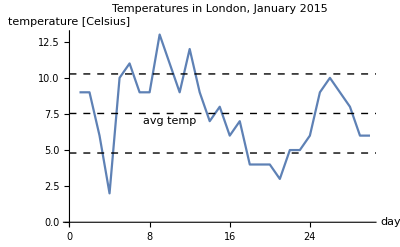

```mathematica
avgTemp = Mean[tempLondon]⟦2⟧ // QuantityMagnitude;
stdDevTemp = StandardDeviation[tempLondon]⟦2⟧ // QuantityMagnitude;
ListLinePlot[tempLondon, 
	PlotLabel->"Temperatures in London, January 2015",
	AxesLabel->{"day", "temperature [Celsius]"},
	Epilog->{Dashed, 
			Line[{{0,avgTemp}, {31,avgTemp}}],
	        Text["avg temp", {10, avgTemp-0.5}],
	        
	        Thin, 
	        Line[{{0,avgTemp+stdDevTemp}, {31,avgTemp+stdDevTemp}}],
	        Line[{{0,avgTemp-stdDevTemp}, {31,avgTemp-stdDevTemp}}]}
]
```

Alternatively, we could indicate the standard deviation by drawing a transparent rectangle:

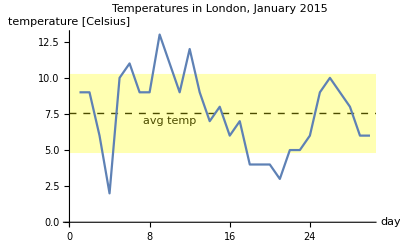

```mathematica
avgTemp = Mean[tempLondon]⟦2⟧ // QuantityMagnitude;
stdDevTemp = StandardDeviation[tempLondon]⟦2⟧ // QuantityMagnitude;
ListLinePlot[tempLondon, 
	PlotLabel->"Temperatures in London, January 2015",
	AxesLabel->{"day", "temperature [Celsius]"},
	Prolog->{Dashed, 
			Line[{{0,avgTemp}, {31,avgTemp}}],
	        Text["avg temp", {10, avgTemp-0.5}],
	        
	        RGBColor[1,1,0,0.3],
	        Rectangle[{0,avgTemp-stdDevTemp}, {31,avgTemp+stdDevTemp}]}
]
```

The fourth argument of RGBColor sets the transparency: 0 means completely transparent (invisible), and 1 means opaque (you cannot see through it, it hides shapes beneath it).

### Challenges

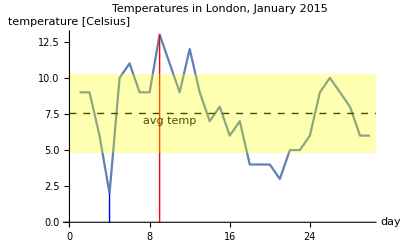
Add lines to the London temperature plot, indicating the times when the maximum and minimum temperatures took place. They should be thin lines, extending from the corresponding data points to the horizontal axis; they should be coloured red for the maximum temperature, and blue for the minimum temperature:

-Graphics-

Hint: Checkout MaximalBy and MinimalBy.

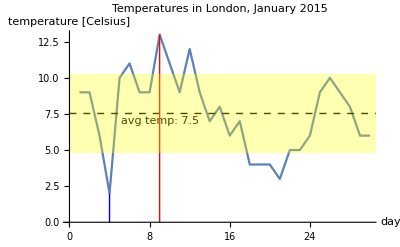
Improve the plot by displaying the average temperature:

-Graphics-

Hint: Use the Row function to display the text.

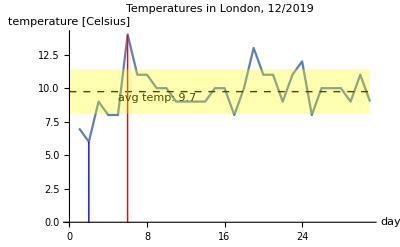
Create the function tempPlot that accepts two arguments: the year and the month. It then plots this same temperature data of London for that year and month.
So tempPlot[2019,7] should result in the following plot:

-Graphics-

## Creating custom plots

Mathematica’s predefined functions use the graphics primitives and directives to draw charts such as scatter plots, line plots, and so on. If Mathematica does not provide a ready-made function to make the plot we want, we can use the graphics primitives and directives to create our own custom plots.

We will demonstrate this by creating a function diskChart that plots a list of quantities as a vertical sequence of disks whose areas are proportional to those quantities. It is similar to a bar chart, but instead of representing quantities by the height of bars, it represents them by the size of disks:

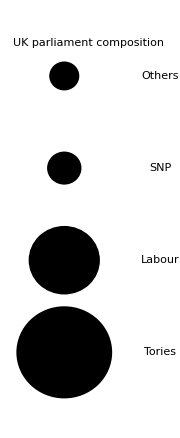

```mathematica
ukParties={"Tories","Labour","SNP","Others"};
ukPartiesNums={365,202,47,36};

diskChart[ukPartiesNums, ukParties, 
          PlotLabel->"UK parliament composition"]
```

The area of a disk of radius r is π r^2. Since we want the area of the circle to represent a quantity x, the corresponding disk must have radius  √(x/π).

One question is: how much space should separate centres of the disks? I choose the spacing to be 2 times the radius of the largest disk, which ensures they do not overlap.

This leads us to the first version of our function:

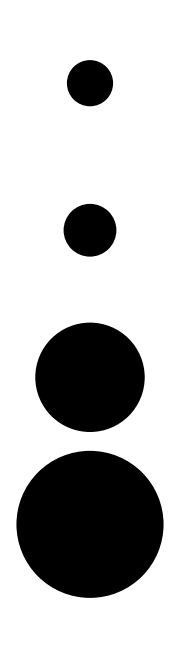

```mathematica
diskChart[data_] := Module[
	{r, dist},
	
	r = Sqrt[data/Pi]; (* radii of the disks *)
	dist = 2 Max[r];          (* distance between disks *)
	
	Graphics[
	    Table[Disk[{0, n dist}, r⟦n⟧], {n, 1, Length[data]}],
		ImageSize->Small
	]
]

ukParties={"Conserv","Labour","SNP","Others"};
ukPartiesNums={365,202,47,36};
diskChart[ukPartiesNums]
```

It would be good to have labels as well, so we extend our function by adding one argument, a list of labels corresponding to each data point. We modify the function to print the label next to each disk, and place the labels at a distance of 2 times the maximum radius, so that they are nicely aligned:

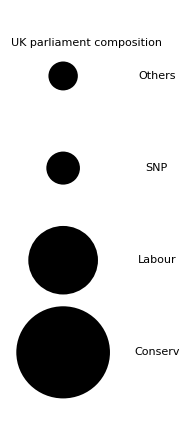

```mathematica
diskChart[data_, labels_, opts:OptionsPattern[Graphics]] := Module[
	{r, dist, labelOffset, disks, lbls},
	
	r = Sqrt[data/Pi]; (* radii of the disks *)
	dist = 2 Max[r];          (* distance between disks *)
	labelOffset = 2 Max[r];
	
	disks = Table[Disk[{0, n dist}, r⟦n⟧], {n, 1, Length[data]}];
	lbls = Table[Text[labels⟦n⟧, {labelOffset, n dist}],
	             {n, 1, Length[data]}];
	
	Graphics[
		{disks, lbls},
		ImageSize->Small,
		opts]
]

ukParties={"Conserv","Labour","SNP","Others"};
ukPartiesNums={365,202,47,36};
diskChart[ukPartiesNums, ukParties, 
          PlotLabel->"UK parliament composition"]
```

### Challenges

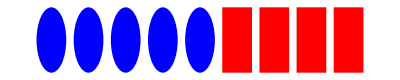
Create the following plot using graphics primitives and directives:

-Graphics-

The circles have radius 0.4, and the squares have side 0.8. The distance between the centres of successive shapes is exactly 1. The centre of the first circle is {0,0}. Hint: use Table to generate sequences of disks and squares.

Create a function diskSquares which takes two arguments, the number of circles and the number of squares. The function returns the list of graphics primitives that make the plot as in the previous challenge.
So Graphics[diskSquares[5,4]] should create the plot shown in challenge 1.

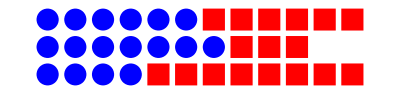
In the version of diskSquares that you created above, the plot always starts at the same location on the screen. Modify the function diskSquares so that it accepts one extra argument, a point {x,y} defining the centre of the first disk. This will allow us to move the plot created above to any location of the screen. This will allow us to stack many plots on the same chart. The command:

	Graphics[{
		diskSquares[4, 8, {0,0}],
		diskSquares[7, 3, {0,1}],
		diskSquares[6, 6, {0,2}]
                  }]

should generate this image:

-Graphics-

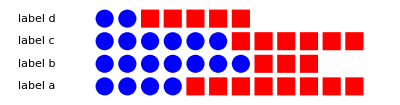
Create a function discSquarePlot so that it does this:

diskSquarePlot[{{4, 8}, {7, 3}, {6, 6}, {2, 5}},
               {“label a”, “label b”,”label c”,”label d”}]

-Graphics-